# Theory/Experiments : Ascorbic Acid - Methylene Blue System

```mathematica
(*Geometrical parameters considering a completely spherical thermal*)
```

```mathematica
s=4*Pi;
```

```mathematica
mg=4/3*Pi;
```

```mathematica
c=1;
```

```mathematica
(*entrainment coefficient*)
```

```mathematica
alpha=0.25;
```

```mathematica
n=3*mg/(s*alpha);
```

```mathematica
(*added mass coefficient*)
```

```mathematica
k=0;
```

```mathematica
(*bc/bw, ratio of the concentration and volume radius*)
```

```mathematica
lambda=0.7;
```

```mathematica
(*Experimental conditions*)
```

```mathematica
v0=10;
```

```mathematica
v430=v0^(4/3);
```

```mathematica
m0=0.00000001;
```

```mathematica
b0=10*981*(1.05-1)/1;
```

```mathematica
Cbinf=0.05*10^(-3);
```

```mathematica
CA0=10^(-3)*10^(-3);
```

```mathematica
na0=CA0*v0;
```

```mathematica
nb0=0;
```

```mathematica
z0=0;
```

```mathematica
(*Reaction conditions*)
```

```mathematica
kr=0
```

0

```mathematica
Grxn=0;
```

```mathematica
(*Environmental conditions*)
```

```mathematica
N2=0;
```

```mathematica
tmax=30
```

30

```mathematica
system={v43'[t]==4/3*s*alpha/(mg^(2/3)*(1+k)*(1-c/n))*Abs[m[t]],m'[t]==b[t],b'[t]==-N2/(1+k)*m[t]+Grxn*kr*na[t]*nb[t]/(v43[t]^(3/4)*lambda^3),na'[t]==-kr*na[t]*Abs[nb[t]]/(v43[t]^(3/4)*lambda^3),nb'[t]==lambda^3*(v43[t]^(-1/4))*s*alpha*Abs[m[t]]*Cbinf/(mg^(2/3)*(1+k)*(1-c/n))-kr*na[t]*nb[t]/(v43[t]^(3/4)*lambda^3),height'[t]==m[t]/(v43[t]^(3/4)*(1+k)*(1-c/n)),v43[0.]==v430,m[0.]==m0,b[0.]==b0,na[0.]==na0,nb[0.]==nb0,height[0.]==z0};
```

```mathematica
sol1=NDSolve[system,{v43,m,b,na,nb,height},{t,0.0001,tmax}]
```

{{v43→InterpolatingFunction[{{0.0001,30.}},<>],m→InterpolatingFunction[{{0.0001,30.}},<>],b→InterpolatingFunction[{{0.0001,30.}},<>],na→InterpolatingFunction[{{0.0001,30.}},<>],nb→InterpolatingFunction[{{0.0001,30.}},<>],height→InterpolatingFunction[{{0.0001,30.}},<>]}}

```mathematica
clear[v4ex,mex,bex,maex,zex];
```

```mathematica
v43ex[t_]=v43[t]/.sol1[[1,1]];
```

```mathematica
mex[t_]=m[t]/.sol1[[1,2]];
```

```mathematica
bex[t_]=b[t]/.sol1[[1,3]];
```

```mathematica
naex[t_]=na[t]/.sol1[[1,4]];
```

```mathematica
nbex[t_]=nb[t]/.sol1[[1,5]];
```

```mathematica
zex[t_]=height[t]/.sol1[[1,6]];
```

```mathematica
vex[t_]=v43ex[t]^(3/4);
```

```mathematica
velocity[t_]=mex[t]/(v43ex[t]*(1+k)*(1-c/n));
```

```mathematica
radius[t_]=vex[t]^(1/3);
```

```mathematica
ca[t_]=naex[t]/vex[t];
cb[t_]=nbex[t]/vex[t];
```

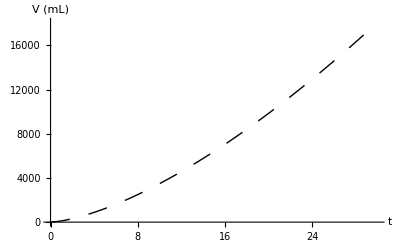
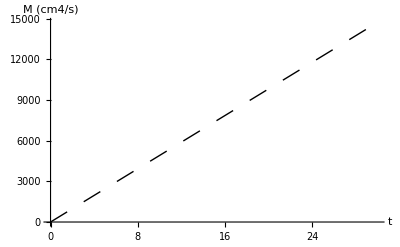
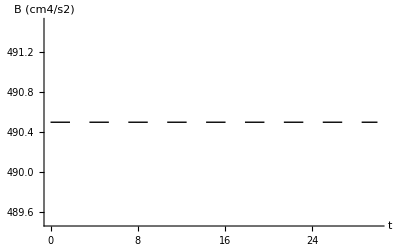
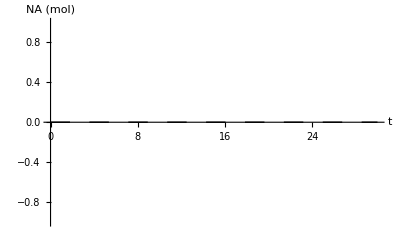
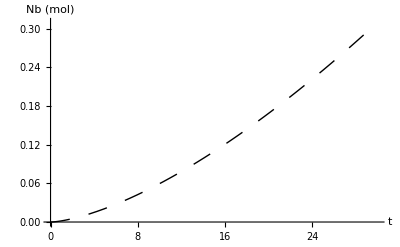
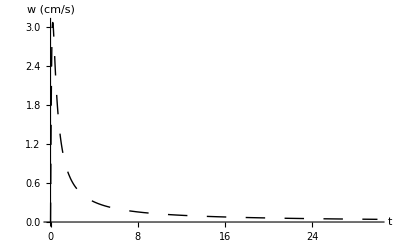
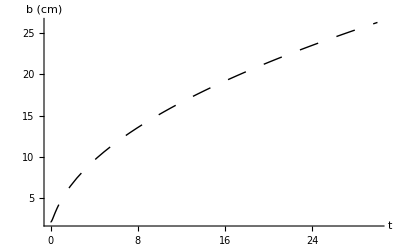
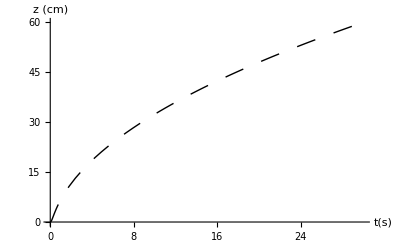

```mathematica
{g1,g2,g3,g4,g5,g6,g7,g8, g9, g10}={Plot[Evaluate[{vex[t]}],{t,0.,tmax}, AxesOrigin->{0,0},PlotRange->All, AxesLabel->{"t","V (mL)"}, PlotStyle->{Dashing[Large],GrayLevel[0.]}],Plot[Evaluate[{mex[t]}],{t,0.,tmax}, AxesOrigin->{0,0},PlotRange->All, AxesLabel->{"t","M (cm4/s)"}, PlotStyle->{Dashing[Large],GrayLevel[0.]}], Plot[Evaluate[{bex[t]}],{t,0.,tmax}, AxesOrigin->{0,0},PlotRange->All, AxesLabel->{"t","B (cm4/s2)"}, PlotStyle->{Dashing[Large],GrayLevel[0.]}],Plot[Evaluate[{naex[t]}],{t,0.,tmax}, AxesOrigin->{0,0},PlotRange->All, AxesLabel->{"t","NA (mol)"}, PlotStyle->{Dashing[Large],GrayLevel[0.]}],Plot[Evaluate[{nbex[t]}],{t,0.,tmax}, AxesOrigin->{0,0},PlotRange->All, AxesLabel->{"t","Nb (mol)"}, PlotStyle->{Dashing[Large],GrayLevel[0.]}],Plot[Evaluate[{velocity[t]}],{t,0.,tmax}, AxesOrigin->{0,0},PlotRange->All, AxesLabel->{"t","w (cm/s)"}, PlotStyle->{Dashing[Large],GrayLevel[0.]}],Plot[Evaluate[{radius[t]}],{t,0.,tmax}, AxesOrigin->{0,0},PlotRange->All, AxesLabel->{"t","b (cm)"}, PlotStyle->{Dashing[Large],GrayLevel[0.]}],Plot[Evaluate[{zex[t]}],{t,0.,tmax}, AxesOrigin->{0,0},PlotRange->All,AxesLabel->{"t(s)","z (cm)"}, PlotStyle->{Dashing[Large],GrayLevel[0.]}],Plot[Evaluate[{ca[t]}],{t,0.,tmax}, AxesOrigin->{0,0},PlotRange->All, AxesLabel->{"t","ca (mol/cm3)"}, PlotStyle->{Dashing[Large],GrayLevel[0.]}],Plot[Evaluate[{cb[t]}],{t,0.,tmax}, AxesOrigin->{0,0},PlotRange->All, AxesLabel->{"t","cb (mol/cm3)"}, PlotStyle->{Dashing[Large],GrayLevel[0.]}]}
```

```mathematica
azero= t/.FindRoot[naex[t]==0,{t,4}]
```

FindRoot::jsing: Encountered a singular Jacobian at the point {t} = {4.`}. Try perturbing the initial point(s).

4.

```mathematica
zex[azero]
```

18.4488

```mathematica
(*Geometrical parameters considering a completely spherical thermal*)
```

```mathematica
s=4*Pi;
```

```mathematica
mg=4/3*Pi;
```

```mathematica
c=1;
```

```mathematica
(*entrainment coefficient*)
```

```mathematica
alpha=0.25;
```

```mathematica
n=3*mg/(s*alpha);
```

```mathematica
(*added mass coefficient*)
```

```mathematica
k=0;
```

```mathematica
(*bc/bw, ratio of the concentration and volume radius*)
```

```mathematica
lambda=0.7;
```

```mathematica
(*Experimental conditions*)
```

```mathematica
v0=10;
```

```mathematica
v430=v0^(4/3);
```

```mathematica
m0=0.00000001;
```

```mathematica
b0=10*981*(1.05-1)/1;
```

```mathematica
Cbinf=0.05*10^(-3);
```

```mathematica
CA0=10^(-3)*10^(-3);
```

```mathematica
na0=CA0*v0;
```

```mathematica
nb0=0;
```

```mathematica
z0=0;
```

```mathematica
(*Reaction conditions*)
```

```mathematica
kr=1*10^3;
```

```mathematica
Grxn=0;
```

```mathematica
(*Environmental conditions*)
```

```mathematica
N2=0;
```

```mathematica
tmax=30
```

30

```mathematica
system={v43'[t]==4/3*s*alpha/(mg^(2/3)*(1+k)*(1-c/n))*Abs[m[t]],m'[t]==b[t],b'[t]==-N2/(1+k)*m[t]+Grxn*kr*na[t]*nb[t]/(v43[t]^(3/4)*lambda^3),na'[t]==-kr*na[t]*Abs[nb[t]]/(v43[t]^(3/4)*lambda^3),nb'[t]==lambda^3*(v43[t]^(-1/4))*s*alpha*Abs[m[t]]*Cbinf/(mg^(2/3)*(1+k)*(1-c/n))-kr*na[t]*nb[t]/(v43[t]^(3/4)*lambda^3),height'[t]==m[t]/(v43[t]^(3/4)*(1+k)*(1-c/n)),v43[0.]==v430,m[0.]==m0,b[0.]==b0,na[0.]==na0,nb[0.]==nb0,height[0.]==z0};
```

```mathematica
sol1=NDSolve[system,{v43,m,b,na,nb,height},{t,0.0001,tmax}]
```

{{v43→InterpolatingFunction[{{0.0001,30.}},<>],m→InterpolatingFunction[{{0.0001,30.}},<>],b→InterpolatingFunction[{{0.0001,30.}},<>],na→InterpolatingFunction[{{0.0001,30.}},<>],nb→InterpolatingFunction[{{0.0001,30.}},<>],height→InterpolatingFunction[{{0.0001,30.}},<>]}}

```mathematica
clear[v4ex,mex,bex,maex,zex];
```

```mathematica
v43ex[t_]=v43[t]/.sol1[[1,1]];
```

```mathematica
mex[t_]=m[t]/.sol1[[1,2]];
```

```mathematica
bex[t_]=b[t]/.sol1[[1,3]];
```

```mathematica
naex[t_]=na[t]/.sol1[[1,4]];
```

```mathematica
nbex[t_]=nb[t]/.sol1[[1,5]];
```

```mathematica
zex[t_]=height[t]/.sol1[[1,6]];
```

```mathematica
vex[t_]=v43ex[t]^(3/4);
```

```mathematica
velocity[t_]=mex[t]/(v43ex[t]*(1+k)*(1-c/n));
```

```mathematica
radius[t_]=vex[t]^(1/3);
```

```mathematica
ca[t_]=naex[t]/vex[t];
cb[t_]=nbex[t]/vex[t];
```

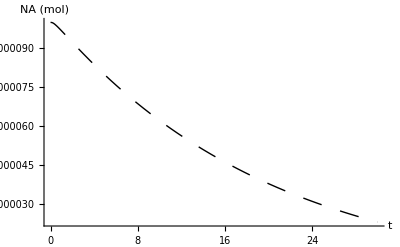
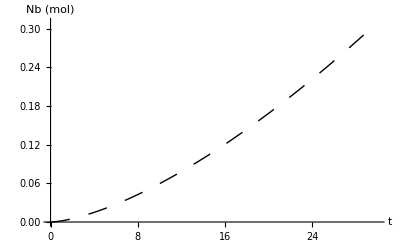
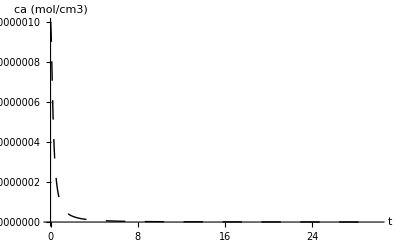
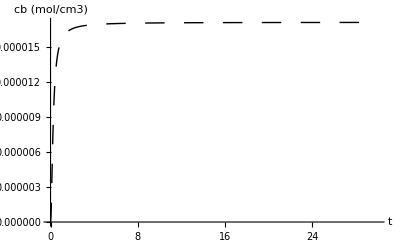
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
{g1,g2,g3,g4,g5,g6,g7,g8, g9, g10}={Plot[Evaluate[{vex[t]}],{t,0.,tmax}, AxesOrigin->{0,0},PlotRange->All, AxesLabel->{"t","V (mL)"}, PlotStyle->{Dashing[Large],GrayLevel[0.]}],Plot[Evaluate[{mex[t]}],{t,0.,tmax}, AxesOrigin->{0,0},PlotRange->All, AxesLabel->{"t","M (cm4/s)"}, PlotStyle->{Dashing[Large],GrayLevel[0.]}], Plot[Evaluate[{bex[t]}],{t,0.,tmax}, AxesOrigin->{0,0},PlotRange->All, AxesLabel->{"t","B (cm4/s2)"}, PlotStyle->{Dashing[Large],GrayLevel[0.]}],Plot[Evaluate[{naex[t]}],{t,0.,tmax}, AxesOrigin->{0,0},PlotRange->All, AxesLabel->{"t","NA (mol)"}, PlotStyle->{Dashing[Large],GrayLevel[0.]}],Plot[Evaluate[{nbex[t]}],{t,0.,tmax}, AxesOrigin->{0,0},PlotRange->All, AxesLabel->{"t","Nb (mol)"}, PlotStyle->{Dashing[Large],GrayLevel[0.]}],Plot[Evaluate[{velocity[t]}],{t,0.,tmax}, AxesOrigin->{0,0},PlotRange->All, AxesLabel->{"t","w (cm/s)"}, PlotStyle->{Dashing[Large],GrayLevel[0.]}],Plot[Evaluate[{radius[t]}],{t,0.,tmax}, AxesOrigin->{0,0},PlotRange->All, AxesLabel->{"t","b (cm)"}, PlotStyle->{Dashing[Large],GrayLevel[0.]}],Plot[Evaluate[{zex[t]}],{t,0.,tmax}, AxesOrigin->{0,0},PlotRange->All,AxesLabel->{"t(s)","z (cm)"}, PlotStyle->{Dashing[Large],GrayLevel[0.]}],Plot[Evaluate[{ca[t]}],{t,0.,tmax}, AxesOrigin->{0,0},PlotRange->All, AxesLabel->{"t","ca (mol/cm3)"}, PlotStyle->{Dashing[Large],GrayLevel[0.]}],Plot[Evaluate[{cb[t]}],{t,0.,tmax}, AxesOrigin->{0,0},PlotRange->All, AxesLabel->{"t","cb (mol/cm3)"}, PlotStyle->{Dashing[Large],GrayLevel[0.]}]}
```

```mathematica
azero= t/.FindRoot[naex[t]==0,{t,4}]
```

InterpolatingFunction::dmval: Input value {44.24752798638514`} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {61.80439630923724`} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction will be suppressed during this calculation.

61.5261

```mathematica
zex[azero]
```

InterpolatingFunction::dmval: Input value {61.526105589175906`} lies outside the range of data in the interpolating function. Extrapolation will be used.

89.9124

```mathematica
(*Geometrical parameters considering a completely spherical thermal*)
```

```mathematica
s=4*Pi;
```

```mathematica
mg=4/3*Pi;
```

```mathematica
c=1;
```

```mathematica
(*entrainment coefficient*)
```

```mathematica
alpha=0.25;
```

```mathematica
n=3*mg/(s*alpha);
```

```mathematica
(*added mass coefficient*)
```

```mathematica
k=0;
```

```mathematica
(*bc/bw, ratio of the concentration and volume radius*)
```

```mathematica
lambda=0.7;
```

```mathematica
(*Experimental conditions*)
```

```mathematica
v0=10;
```

```mathematica
v430=v0^(4/3);
```

```mathematica
m0=0.00000001;
```

```mathematica
b0=10*981*(1.05-1)/1;
```

```mathematica
Cbinf=0.05*10^(-3);
```

```mathematica
CA0=10^(-4)*10^(-3);
```

```mathematica
na0=CA0*v0;
```

```mathematica
nb0=0;
```

```mathematica
z0=0;
```

```mathematica
(*Reaction conditions*)
```

```mathematica
kr=0;
```

```mathematica
Grxn=0;
```

```mathematica
(*Environmental conditions*)
```

```mathematica
N2=0;
```

```mathematica
tmax=30
```

30

```mathematica
system={v43'[t]==4/3*s*alpha/(mg^(2/3)*(1+k)*(1-c/n))*Abs[m[t]],m'[t]==b[t],b'[t]==-N2/(1+k)*m[t]+Grxn*kr*na[t]*nb[t]/(v43[t]^(3/4)*lambda^3),na'[t]==-kr*na[t]*Abs[nb[t]]/(v43[t]^(3/4)*lambda^3),nb'[t]==lambda^3*(v43[t]^(-1/4))*s*alpha*Abs[m[t]]*Cbinf/(mg^(2/3)*(1+k)*(1-c/n))-kr*na[t]*nb[t]/(v43[t]^(3/4)*lambda^3),height'[t]==m[t]/(v43[t]^(3/4)*(1+k)*(1-c/n)),v43[0.]==v430,m[0.]==m0,b[0.]==b0,na[0.]==na0,nb[0.]==nb0,height[0.]==z0};
```

```mathematica
sol1=NDSolve[system,{v43,m,b,na,nb,height},{t,0.0001,tmax}]
```

{{v43→InterpolatingFunction[{{0.0001,30.}},<>],m→InterpolatingFunction[{{0.0001,30.}},<>],b→InterpolatingFunction[{{0.0001,30.}},<>],na→InterpolatingFunction[{{0.0001,30.}},<>],nb→InterpolatingFunction[{{0.0001,30.}},<>],height→InterpolatingFunction[{{0.0001,30.}},<>]}}

```mathematica
clear[v4ex,mex,bex,maex,zex];
```

```mathematica
v43ex[t_]=v43[t]/.sol1[[1,1]];
```

```mathematica
mex[t_]=m[t]/.sol1[[1,2]];
```

```mathematica
bex[t_]=b[t]/.sol1[[1,3]];
```

```mathematica
naex[t_]=na[t]/.sol1[[1,4]];
```

```mathematica
nbex[t_]=nb[t]/.sol1[[1,5]];
```

```mathematica
zex[t_]=height[t]/.sol1[[1,6]];
```

```mathematica
vex[t_]=v43ex[t]^(3/4);
```

```mathematica
velocity[t_]=mex[t]/(v43ex[t]*(1+k)*(1-c/n));
```

```mathematica
radius[t_]=vex[t]^(1/3);
```

```mathematica
ca[t_]=naex[t]/vex[t];
cb[t_]=nbex[t]/vex[t];
```

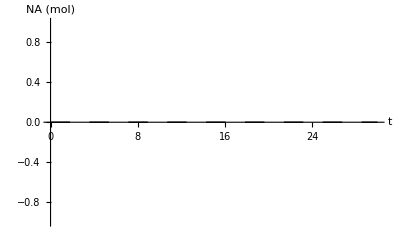
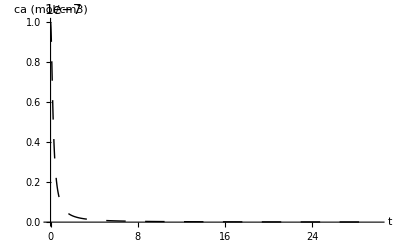
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
{g1,g2,g3,g4,g5,g6,g7,g8, g9, g10}={Plot[Evaluate[{vex[t]}],{t,0.,tmax}, AxesOrigin->{0,0},PlotRange->All, AxesLabel->{"t","V (mL)"}, PlotStyle->{Dashing[Large],GrayLevel[0.]}],Plot[Evaluate[{mex[t]}],{t,0.,tmax}, AxesOrigin->{0,0},PlotRange->All, AxesLabel->{"t","M (cm4/s)"}, PlotStyle->{Dashing[Large],GrayLevel[0.]}], Plot[Evaluate[{bex[t]}],{t,0.,tmax}, AxesOrigin->{0,0},PlotRange->All, AxesLabel->{"t","B (cm4/s2)"}, PlotStyle->{Dashing[Large],GrayLevel[0.]}],Plot[Evaluate[{naex[t]}],{t,0.,tmax}, AxesOrigin->{0,0},PlotRange->All, AxesLabel->{"t","NA (mol)"}, PlotStyle->{Dashing[Large],GrayLevel[0.]}],Plot[Evaluate[{nbex[t]}],{t,0.,tmax}, AxesOrigin->{0,0},PlotRange->All, AxesLabel->{"t","Nb (mol)"}, PlotStyle->{Dashing[Large],GrayLevel[0.]}],Plot[Evaluate[{velocity[t]}],{t,0.,tmax}, AxesOrigin->{0,0},PlotRange->All, AxesLabel->{"t","w (cm/s)"}, PlotStyle->{Dashing[Large],GrayLevel[0.]}],Plot[Evaluate[{radius[t]}],{t,0.,tmax}, AxesOrigin->{0,0},PlotRange->All, AxesLabel->{"t","b (cm)"}, PlotStyle->{Dashing[Large],GrayLevel[0.]}],Plot[Evaluate[{zex[t]}],{t,0.,tmax}, AxesOrigin->{0,0},PlotRange->All,AxesLabel->{"t(s)","z (cm)"}, PlotStyle->{Dashing[Large],GrayLevel[0.]}],Plot[Evaluate[{ca[t]}],{t,0.,tmax}, AxesOrigin->{0,0},PlotRange->All, AxesLabel->{"t","ca (mol/cm3)"}, PlotStyle->{Dashing[Large],GrayLevel[0.]}],Plot[Evaluate[{cb[t]}],{t,0.,tmax}, AxesOrigin->{0,0},PlotRange->All, AxesLabel->{"t","cb (mol/cm3)"}, PlotStyle->{Dashing[Large],GrayLevel[0.]}]}
```

```mathematica
azero= t/.FindRoot[naex[t]==0,{t,4}]
```

FindRoot::jsing: Encountered a singular Jacobian at the point {t} = {4.`}. Try perturbing the initial point(s).

4.

```mathematica
zex[azero]
```

18.4488

```mathematica
(*Geometrical parameters considering a completely spherical thermal*)
```

```mathematica
s=4*Pi;
```

```mathematica
mg=4/3*Pi;
```

```mathematica
c=1;
```

```mathematica
(*entrainment coefficient*)
```

```mathematica
alpha=0.25;
```

```mathematica
n=3*mg/(s*alpha);
```

```mathematica
(*added mass coefficient*)
```

```mathematica
k=0;
```

```mathematica
(*bc/bw, ratio of the concentration and volume radius*)
```

```mathematica
lambda=0.7;
```

```mathematica
(*Experimental conditions*)
```

```mathematica
v0=10;
```

```mathematica
v430=v0^(4/3);
```

```mathematica
m0=0.00000001;
```

```mathematica
b0=10*981*(1.05-1)/1;
```

```mathematica
Cbinf=0.05*10^(-3);
```

```mathematica
CA0=10^(-4)*10^(-3);
```

```mathematica
na0=CA0*v0;
```

```mathematica
nb0=0;
```

```mathematica
z0=0;
```

```mathematica
(*Reaction conditions*)
```

```mathematica
kr=1*10^3;
```

```mathematica
Grxn=0;
```

```mathematica
(*Environmental conditions*)
```

```mathematica
N2=0;
```

```mathematica
tmax=14
```

14

```mathematica
system={v43'[t]==4/3*s*alpha/(mg^(2/3)*(1+k)*(1-c/n))*Abs[m[t]],m'[t]==b[t],b'[t]==-N2/(1+k)*m[t]+Grxn*kr*na[t]*nb[t]/(v43[t]^(3/4)*lambda^3),na'[t]==-kr*na[t]*Abs[nb[t]]/(v43[t]^(3/4)*lambda^3),nb'[t]==lambda^3*(v43[t]^(-1/4))*s*alpha*Abs[m[t]]*Cbinf/(mg^(2/3)*(1+k)*(1-c/n))-kr*na[t]*nb[t]/(v43[t]^(3/4)*lambda^3),height'[t]==m[t]/(v43[t]^(3/4)*(1+k)*(1-c/n)),v43[0.]==v430,m[0.]==m0,b[0.]==b0,na[0.]==na0,nb[0.]==nb0,height[0.]==z0};
```

```mathematica
sol1=NDSolve[system,{v43,m,b,na,nb,height},{t,0.0001,tmax}]
```

{{v43→InterpolatingFunction[{{0.0001,14.}},<>],m→InterpolatingFunction[{{0.0001,14.}},<>],b→InterpolatingFunction[{{0.0001,14.}},<>],na→InterpolatingFunction[{{0.0001,14.}},<>],nb→InterpolatingFunction[{{0.0001,14.}},<>],height→InterpolatingFunction[{{0.0001,14.}},<>]}}

```mathematica
clear[v4ex,mex,bex,maex,zex];
```

```mathematica
v43ex[t_]=v43[t]/.sol1[[1,1]];
```

```mathematica
mex[t_]=m[t]/.sol1[[1,2]];
```

```mathematica
bex[t_]=b[t]/.sol1[[1,3]];
```

```mathematica
naex[t_]=na[t]/.sol1[[1,4]];
```

```mathematica
nbex[t_]=nb[t]/.sol1[[1,5]];
```

```mathematica
zex[t_]=height[t]/.sol1[[1,6]];
```

```mathematica
vex[t_]=v43ex[t]^(3/4);
```

```mathematica
velocity[t_]=mex[t]/(v43ex[t]*(1+k)*(1-c/n));
```

```mathematica
radius[t_]=vex[t]^(1/3);
```

```mathematica
ca[t_]=naex[t]/vex[t];
cb[t_]=nbex[t]/vex[t];
```

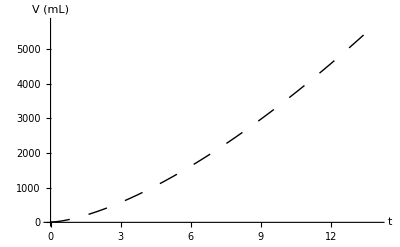
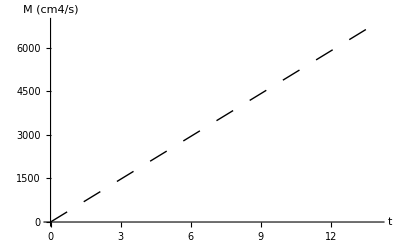
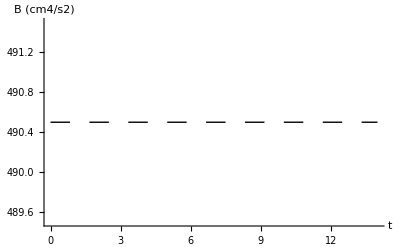
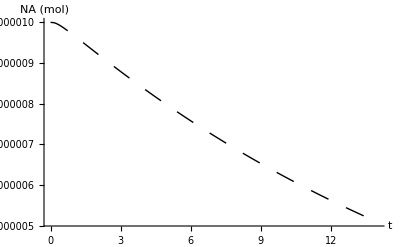
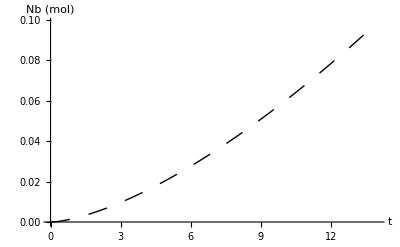
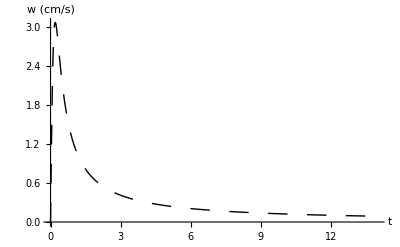
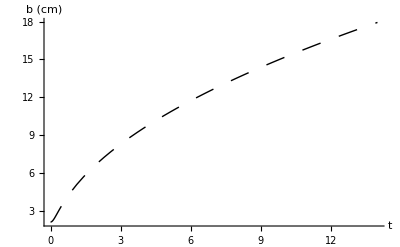
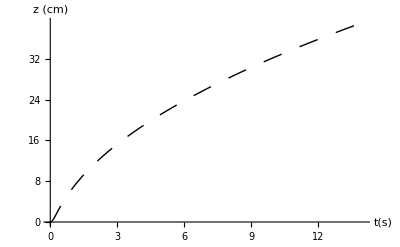

```mathematica
{g1,g2,g3,g4,g5,g6,g7,g8, g9, g10}={Plot[Evaluate[{vex[t]}],{t,0.,tmax}, AxesOrigin->{0,0},PlotRange->All, AxesLabel->{"t","V (mL)"}, PlotStyle->{Dashing[Large],GrayLevel[0.]}],Plot[Evaluate[{mex[t]}],{t,0.,tmax}, AxesOrigin->{0,0},PlotRange->All, AxesLabel->{"t","M (cm4/s)"}, PlotStyle->{Dashing[Large],GrayLevel[0.]}], Plot[Evaluate[{bex[t]}],{t,0.,tmax}, AxesOrigin->{0,0},PlotRange->All, AxesLabel->{"t","B (cm4/s2)"}, PlotStyle->{Dashing[Large],GrayLevel[0.]}],Plot[Evaluate[{naex[t]}],{t,0.,tmax}, AxesOrigin->{0,0},PlotRange->All, AxesLabel->{"t","NA (mol)"}, PlotStyle->{Dashing[Large],GrayLevel[0.]}],Plot[Evaluate[{nbex[t]}],{t,0.,tmax}, AxesOrigin->{0,0},PlotRange->All, AxesLabel->{"t","Nb (mol)"}, PlotStyle->{Dashing[Large],GrayLevel[0.]}],Plot[Evaluate[{velocity[t]}],{t,0.,tmax}, AxesOrigin->{0,0},PlotRange->All, AxesLabel->{"t","w (cm/s)"}, PlotStyle->{Dashing[Large],GrayLevel[0.]}],Plot[Evaluate[{radius[t]}],{t,0.,tmax}, AxesOrigin->{0,0},PlotRange->All, AxesLabel->{"t","b (cm)"}, PlotStyle->{Dashing[Large],GrayLevel[0.]}],Plot[Evaluate[{zex[t]}],{t,0.,tmax}, AxesOrigin->{0,0},PlotRange->All,AxesLabel->{"t(s)","z (cm)"}, PlotStyle->{Dashing[Large],GrayLevel[0.]}],Plot[Evaluate[{ca[t]}],{t,0.,tmax}, AxesOrigin->{0,0},PlotRange->All, AxesLabel->{"t","ca (mol/cm3)"}, PlotStyle->{Dashing[Large],GrayLevel[0.]}],Plot[Evaluate[{cb[t]}],{t,0.,tmax}, AxesOrigin->{0,0},PlotRange->All, AxesLabel->{"t","cb (mol/cm3)"}, PlotStyle->{Dashing[Large],GrayLevel[0.]}]}
```

```mathematica
azero= t/.FindRoot[naex[t]==0,{t,13}]
```

InterpolatingFunction::dmval: Input value {33.03896417381387`} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {47.48757533460418`} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction will be suppressed during this calculation.

46.1613

```mathematica
zex[azero]
```

InterpolatingFunction::dmval: Input value {46.161261135909726`} lies outside the range of data in the interpolating function. Extrapolation will be used.

95.7539